# Moran indices for simulations (rule-based and ODE-based)

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
fontOption="Arial";
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->All,
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Moran index for rule-based models

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"ResultsAll"}]];
```

These are 5 data sets that represent the 5 repetitions for the random, the nearest neighbour and the local clustering model. With respect to period two, the files are identical.

```mathematica
data=Flatten[Import[#]&/@finalFNames,1];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

```mathematica
Keys[nucleiFeatures[[1,1]]]
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Total-Avg,Total-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Total-AvgLnCorr,SurfaceDistance,SurfaceNearest,PCGNeighborCount,PCGClusteringCoefficient,PCGMinNeighborDistance,PCGMaxNeighborDistance,PCGMeanNeighborDistance,PCGStandardDeviationNeighborDistance,DCGNeighborCount,DCGClusteringCoefficient,DCGMinNeighborDistance,DCGMaxNeighborDistance,DCGMeanNeighborDistance,DCGStandardDeviationNeighborDistance,Dapi-AvgNorm,Nanog-AvgNorm,Gata6-AvgNorm,Total-AvgNorm,Dapi-AvgNorm,Nanog-AvgNorm,Gata6-AvgNorm,Total-AvgNorm,Nanog-AvgShifted,Gata6-AvgShifted,Quadrant,randomFateN,nearestNeighFateN,periodTwoIFateN,periodTwoIIFateN,localClusterFate0.1N,randomFateG6,nearestNeighFateG6,periodTwoIFateG6,periodTwoIIFateG6,localClusterFate0.1G6}

```mathematica
Length[nucleiFeatures]/5
```

2214

### Random model

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","Embryo","Experiment","N+-Moran","G6+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({valuesN,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"N+","randomFateN"];If [Length[DeleteDuplicates[valuesN]]>1,calcMoranI[valuesN,weights],"only one cell type"]),
({valuesG6,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"G6+","randomFateG6"];If [Length[DeleteDuplicates[valuesG6]]>1,calcMoranI[valuesG6,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesRandom.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesRandom.mx"}]];
```

number of embryos discarded for NANOG

```mathematica
Length[Cases["N+-Moran"/.moranValues,"only one cell type"]]
```

315

number of embryos discarded for GATA6

```mathematica
Length[Cases["G6+-Moran"/.moranValues,"only one cell type"]]
```

500

```mathematica
Length[Cases["G6+-Moran"/.moranValues,Except["only one cell type"]]]
```

3190

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{1630,1090,885}

```mathematica
#/5&/@(Length/@moranValuesByStage)
```

{326,218,177}

```mathematica
Total[Length/@moranValuesByStage]
```

3605

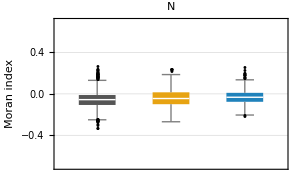
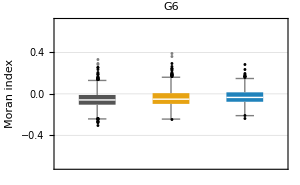

```mathematica
plotMoran=Row[Table[BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@(i/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@StringDelete[i,"+-Moran"],ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]],{i,{"N+-Moran","G6+-Moran"}}],"    "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_Random.png"}],plotMoran]
```

### Alternating model

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","Embryo","Experiment","N+-Moran","G6+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({valuesN,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"N+","nearestNeighFateN"];If [Length[DeleteDuplicates[valuesN]]>1,calcMoranI[valuesN,weights],"only one cell type"]),
({valuesG6,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"G6+","nearestNeighFateG6"];If [Length[DeleteDuplicates[valuesG6]]>1,calcMoranI[valuesG6,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesAlternating.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesAlternating.mx"}]];
```

number of embryos discarded for NANOG

```mathematica
Length[Cases["N+-Moran"/.moranValues,"only one cell type"]]
```

0

number of embryos discarded for GATA6

```mathematica
Length[Cases["G6+-Moran"/.moranValues,"only one cell type"]]
```

0

```mathematica
Length[Cases["G6+-Moran"/.moranValues,Except["only one cell type"]]]
```

3690

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{1630,1090,885}

```mathematica
#/5&/@(Length/@moranValuesByStage)
```

{326,218,177}

```mathematica
Total[Length/@moranValuesByStage]
```

3605

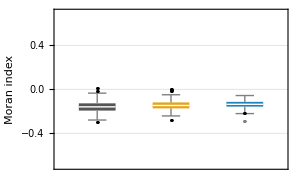

```mathematica
plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("N+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_Alternating.png"}],plotMoran]
```

### Local cluster model p=0.55 (see also LocalClusteringScan.nb)

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","Embryo","Experiment","N+-Moran","G6+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({valuesN,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"N+","localClusterFate0.1N"];If [Length[DeleteDuplicates[valuesN]]>1,calcMoranI[valuesN,weights],"only one cell type"]),
({valuesG6,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"G6+","localClusterFate0.1G6"];If [Length[DeleteDuplicates[valuesG6]]>1,calcMoranI[valuesG6,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesLocalClust0.55.mx"}],moranValues]*)
```

```mathematica
moranValuesAll=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesLocalClust0.55.mx"}]];
```

```mathematica
moranValues=("p=0.55"/.moranValuesAll);
```

number of embryos discarded

```mathematica
Length[Cases["+-Moran"/.moranValues,"only one cell type"]]
```

3

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{1630,1090,885}

```mathematica
#/5&/@(Length/@moranValuesByStage)
```

{326,218,177}

```mathematica
Total[Length/@moranValuesByStage]
```

3605

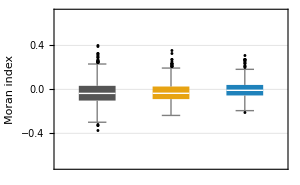

```mathematica
plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_Cluster055.png"}],plotMoran]
```

### Period Two I

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","Embryo","Experiment","N+-Moran","G6+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({valuesN,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"N+","periodTwoIFateN"];If [Length[DeleteDuplicates[valuesN]]>1,calcMoranI[valuesN,weights],"only one cell type"]),
({valuesG6,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"G6+","periodTwoIFateG6"];If [Length[DeleteDuplicates[valuesG6]]>1,calcMoranI[valuesG6,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesPeriodTwoI.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesPeriodTwoI.mx"}]];
```

number of embryos discarded for NANOG

```mathematica
Length[Cases["N+-Moran"/.moranValues,"only one cell type"]]
```

0

number of embryos discarded for GATA6

```mathematica
Length[Cases["G6+-Moran"/.moranValues,"only one cell type"]]
```

0

```mathematica
Length[Cases["G6+-Moran"/.moranValues,Except["only one cell type"]]]
```

3690

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{1630,1090,885}

```mathematica
#/5&/@(Length/@moranValuesByStage)
```

{326,218,177}

```mathematica
Total[Length/@moranValuesByStage]
```

3605

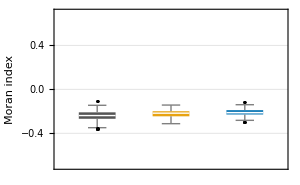

```mathematica
plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("N+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_PeriodTwoI.png"}],plotMoran]
```

### Combine all rule-based in one figure

```mathematica
moranValuesRandom=(Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesRandom.mx"}]]);
```

```mathematica
moranValuesNearestNeigh=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesAlternating.mx"}]]/.(Rule["N+-Moran",a_]->Rule["+-Moran",a]);
```

```mathematica
moranValuesAll=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesLocalClust0.55.mx"}]];
```

```mathematica
moranValuesLocalClust=("p=0.55"/.moranValuesAll);
```

```mathematica
moranValuesPeriodTwoI=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesPeriodTwoI.mx"}]]/.(Rule["N+-Moran",a_]->Rule["+-Moran",a]);
```

```mathematica
moranValuesRandom[[1]]
```

{Stage→4.,Embryo→10YNDembr1.ome,Experiment→Batch9,N+-Moran→0.0666667,G6+-Moran→0.00334448}

```mathematica
moranValuesNearestNeigh[[1]]
```

{Stage→4.,Embryo→10YNDembr1.ome,Experiment→Batch9,+-Moran→-0.173913,G6+-Moran→-0.173913}

```mathematica
moranValuesLocalClust[[1]]
```

{Stage→4.,Embryo→10YNDembr1.ome,Experiment→Batch9,+-Moran→-0.0310559}

```mathematica
moranValuesPeriodTwoI[[1]]
```

{Stage→4.,Embryo→10YNDembr1.ome,Experiment→Batch9,+-Moran→-0.144928,G6+-Moran→-0.144928}

```mathematica
plotData=Join[Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&]),{i,{moranValuesPeriodTwoI,moranValuesNearestNeigh,moranValuesLocalClust}}],{Cases[#,Except["only one cell type"]]&@("N+-Moran"/.Select[moranValuesRandom,("Stage"/.#)>3.0&]),Cases[#,Except["only one cell type"]]&@("G6+-Moran"/.Select[moranValuesRandom,("Stage"/.#)>3.0&])}];
```

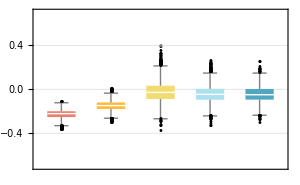

```mathematica
moranIndexAll=BoxWhiskerChart[plotData,"Outliers",(*ChartLabels->(Rotate[#,90°]&/@{"Random","Alternating","Local clustering","Period two","Nearest neighbour signalling"}),*)ImageSize->300,PlotRange->{-0.7,0.7},ChartStyle->24,FrameLabel-> {None,"Moran's index"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moranValuesAllSim.png"}],moranIndexAll]
```

```mathematica
legendMoranValuesAllSim=SwatchLegend[ColorData[24][#]&/@Range[5],{"Checkerboard","Alternating","Local clustering (p=0.55)","Random NANOG","Random GATA6"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","legendMoranValuesAllSim.png"}],legendMoranValuesAllSim]
```

```mathematica
exportDataForHypothesisTest=Join@@@Transpose[{Partition[{"PeriodTwo","Alternating","LocalCluster055","RandomNANOG","RandomGATA6"},1],plotData}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","ruleBasedModeldataForWelchTest.json"}],exportDataForHypothesisTest]
```

## Moran index for nearest neighbour signalling

### No cell division

```mathematica
(*simFolder=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\simulations")];*)
```

```mathematica
(*finalFNames=FileNameJoin[{simFolder,"TissueFeatures","ICMCoordinates_with_fates.mx"}];*)
```

```mathematica
(*data=Import@finalFNames;*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","EmbryoRunningID","SimulationID","+-Moran"},#}]&/@(Table[Join[{"Stage","EmbryoRunningID","SimulationID"}/.staging[[i]],{({valuesP,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"+","Quadrant"];If [Length[DeleteDuplicates[valuesP]]>1,calcMoranI[valuesP,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignal.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignal.mx"}]];
```

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{32400,21400,17000}

```mathematica
#/100&/@(Length/@moranValuesByStage)
```

{324,214,170}

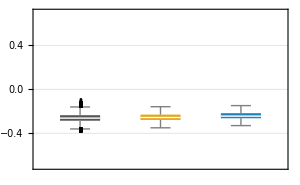

```mathematica
plotMoranByStage=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_NNByStage.png"}],plotMoranByStage]
```

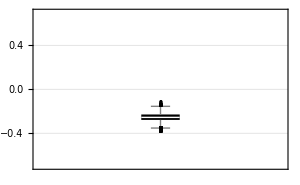

```mathematica
plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValues,("Stage"/.#)>3.0&]),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{{-0.25,2.25},{-0.7,0.7}},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_NN.png"}],plotMoran]
```

### With cell division

```mathematica
(*simFolder=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\simulations")];*)
```

```mathematica
(*finalFNames=Select[FileNames["ICMNumCellDiv_*.mx",FileNameJoin[{simFolder,"TissueFeatures\\simulated_embryo_stages\\"}]],StringContainsQ[#,"NN"]==True&];*)
```

```mathematica
(*data=Flatten[Import/@finalFNames,1];*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","EmbryoRunningID","SimulationID","+-Moran"},#}]&/@(Table[Join[{"Stage","EmbryoRunningID","SimulationID"}/.staging[[i]],{({valuesP,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"+","Quadrant"];If [Length[DeleteDuplicates[valuesP]]>1,calcMoranI[valuesP,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignalCD.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignalCD.mx"}]];
```

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{200,200,200}

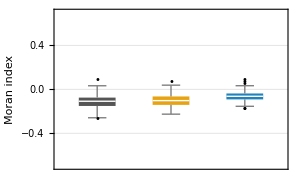

```mathematica
plotMoranByStage=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_NNCellDivByStage.png"}],plotMoranByStage]
```

```mathematica
plotDataByStage=Cases[#,Except["only one cell type"]]&/@("+-Moran"/.moranValuesByStage);
```

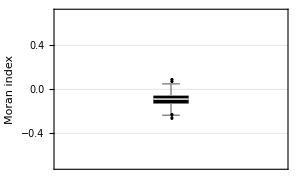

```mathematica
plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValues,("Stage"/.#)>3.0&]),"Outliers",ChartLabels->{{"early","mid","late"},None},ImageSize->300,PlotRange->{{-0.25,2.25},{-0.7,0.7}},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_NNCellDiv.png"}],plotMoran]
```

## Moran index for distance-based signalling

### No cell division

```mathematica
(*simFolder=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\simulations")];*)
```

```mathematica
(*finalFNames=FileNameJoin[{simFolder,"TissueFeatures","ICMCoordinates_with_fates_global_signaling.mx"}];*)
```

```mathematica
(*data=Import@finalFNames;*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","EmbryoRunningID","SimulationID","Range_q","+-Moran"},#}]&/@(Table[Join[{"Stage","EmbryoRunningID","SimulationID","Range_q"}/.staging[[i]],{({valuesP,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"+","Quadrant"];If [Length[DeleteDuplicates[valuesP]]>1,calcMoranI[valuesP,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal.mx"}]];
```

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{32400,21400,17000}

```mathematica
#/100&/@(Length/@moranValuesByStage)
```

{324,214,170}

```mathematica
rangeMoranByStages=Table[{"Range_q","+-Moran"}/.moranValuesByStage[[i]],{i,1,3}];
```

```mathematica
avgMoran={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValues,("Stage"/.#)>3.0&],{0,1,0.1},{-10^6,10^6,2*10^6}],1],Length[#]>0&]);
```

```mathematica
black[i_]:={Black}[[i]]
```

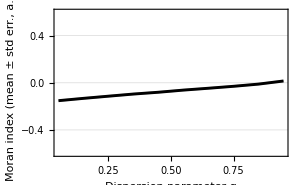

```mathematica
plotMoran=Show[{plotMeanStdLighter[{#[[All,1]]&@avgMoran},{#[[All,2;;3]]&@avgMoran},0,"Dispersion parameter q","Moran index\n(mean ± std err., a.u.)",black]},PlotRange->{-0.6,0.6},ImageSize->300,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_DistSig.png"}],plotMoran]
```

```mathematica
avgMoranByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[{"Range_q","+-Moran"}/.moranValuesByStage[[i]],{0,1,0.1},{-10^6,10^6,2*10^6}],1],Length[#]>0&]),{i,1,3}];
```

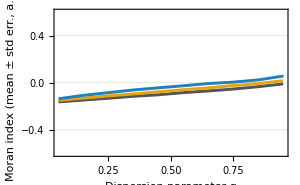

```mathematica
plotMoranByStage=(*Labeled[*)Show[{plotMeanStdLighter[#[[All,1]]&/@avgMoranByStages,#[[All,2;;3]]&/@avgMoranByStages,0,"Dispersion parameter q","Moran index\n(mean ± std err., a.u.)",colour3]},PlotRange->{-0.6,0.6},ImageSize->300,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_DistSigByStage.png"}],plotMoranByStage]
```

### With cell division

```mathematica
(*simFolder=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\simulations")];*)
```

```mathematica
(*finalFNames=Select[FileNames["ICMNumCellDiv_*.mx"|"*(1000 organoids)*.mx",FileNameJoin[{simFolder,"TissueFeatures\\simulated_embryo_stages\\"}]],StringContainsQ[#,"NN"]==False&];*)
```

```mathematica
(*data=Flatten[Import/@finalFNames,1];*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValues=MapThread[Rule,{{"Stage","EmbryoRunningID","SimulationID","Range_q","+-Moran"},#}]&/@(Table[Join[{"Stage","EmbryoRunningID","SimulationID","Range_q"}/.staging[[i]],{({valuesP,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"v+","Quadrant"];If [Length[DeleteDuplicates[valuesP]]>1,calcMoranI[valuesP,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}]);*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal_CD.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal_CD.mx"}]];
```

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{1200,1200,1200}

```mathematica
#/100&/@(Length/@moranValuesByStage)
```

{12,12,12}

```mathematica
rangeMoranByStages=Table[{"Range_q","+-Moran"}/.moranValuesByStage[[i]],{i,1,3}];
```

```mathematica
avgMoran={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValues,("Stage"/.#)>3.0&],{0,1,0.1},{-10^6,10^6,2*10^6}],1],Length[#]>0&]);
```

```mathematica
black[i_]:={Black}[[i]]
```

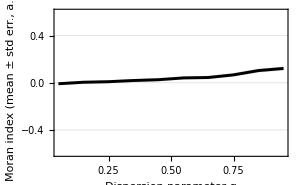

```mathematica
plotAvgMoran=Show[{plotMeanStdLighter[{#[[All,1]]&@avgMoran},{#[[All,2;;3]]&@avgMoran},0,"Dispersion parameter q","Moran index\n(mean ± std err., a.u.)",black]},PlotRange->{-0.6,0.6},ImageSize->300,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_DistSigDivision_Avg.png"}],plotAvgMoran]
```

```mathematica
avgMoranByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[{"Range_q","+-Moran"}/.moranValuesByStage[[i]],{0,1,0.1},{-10^6,10^6,2*10^6}],1],Length[#]>0&]),{i,1,3}];
```

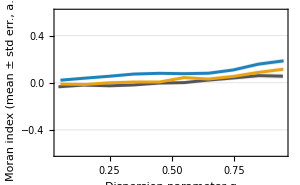

```mathematica
plotAvgMoranByStages=(*Labeled[*)Show[{plotMeanStdLighter[#[[All,1]]&/@avgMoranByStages,#[[All,2;;3]]&/@avgMoranByStages,0,"Dispersion parameter q","Moran index\n(mean ± std err., a.u.)",colour3]},PlotRange->{-0.6,0.6},ImageSize->300,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_DistSigDivision_Stages.png"}],plotAvgMoranByStages]
```

## Moran index for signalling models

```mathematica
moranValuesNN=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignal.mx"}]];
```

```mathematica
moranValuesNNCD=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesNNSignalCD.mx"}]];
```

```mathematica
moranValuesDBRaw=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal.mx"}]];
```

```mathematica
moranValuesDBCDRaw=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesDistSignal_CD.mx"}]];
```

#### Nearest neighbour

```mathematica
plotDataNN=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&]),{i,{moranValuesNN,moranValuesNNCD}}];
```

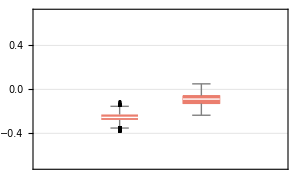

```mathematica
BoxWhiskerChart[plotDataNN,"Outliers",ImageSize->300,PlotRange->{{0,3},{-0.7,0.7}},ChartStyle->{24,{EdgeForm[None],EdgeForm[Thick]}},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

### Distance-based

```mathematica
moranValuesDB=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBRaw,("Stage"/.#)>3.0&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
moranValuesDBCD=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBCDRaw,("Stage"/.#)>3.0&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
plotDataDB=Table[{moranValuesDB[[i,All,2]],moranValuesDBCD[[i,All,2]]},{i,1,Length[moranValuesDB]}];
```

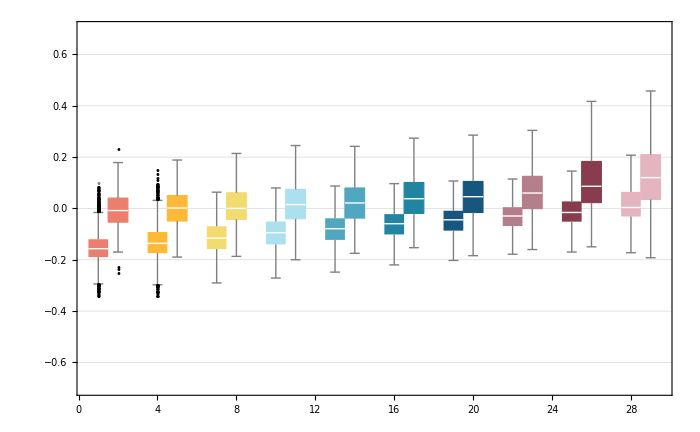

```mathematica
BoxWhiskerChart[plotDataDB,{"Outliers"},ImageSize->700,PlotRange->{-0.7,0.7},ChartStyle->{24,{EdgeForm[None],EdgeForm[Thick]}},ChartLabels->{ToString/@Range[0.05,0.95,0.1],None},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]],BarSpacing->{0,1}]
```

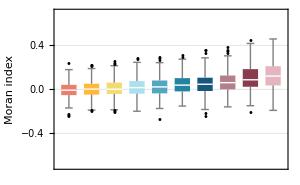

```mathematica
BoxWhiskerChart[#[[All,2]]&/@moranValuesDBCD,"Outliers",ImageSize->300,PlotRange->{-0.7,0.7},ChartStyle->24,FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

### All (only early and mid stage)

```mathematica
colourMoran[i_]:=Join[{Gray},ColorData[24]/@Range[10]][[i]]
```

```mathematica
plotDataNN=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&]),{i,{moranValuesNN,moranValuesNNCD}}];
```

```mathematica
plotDataNNEM=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&]),{i,{moranValuesNN,moranValuesNNCD}}];
```

```mathematica
moranValuesDBEM=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBRaw,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
moranValuesDBCDEM=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBCDRaw,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
plotDataDBEM=Table[{moranValuesDBEM[[i,All,2]],moranValuesDBCDEM[[i,All,2]]},{i,1,Length[moranValuesDBEM]}];
```

```mathematica
plotDataAllEM=Join[{plotDataNNEM},plotDataDBEM];
```

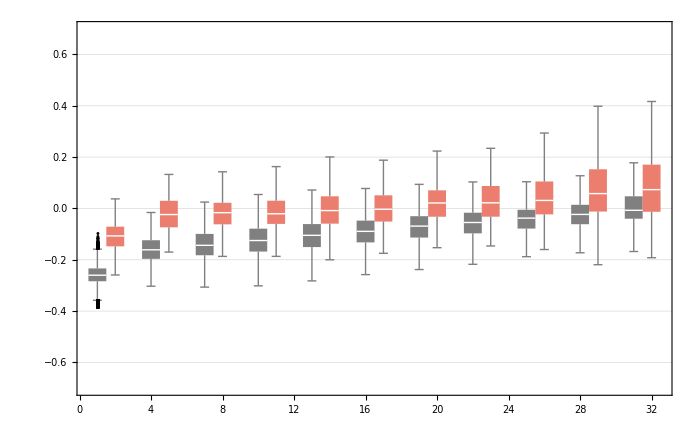

```mathematica
moranIndexSigEM=BoxWhiskerChart[plotDataAllEM,{"Outliers"},ImageSize->700,PlotRange->{-0.7,0.7},ChartStyle->colourMoran/@Range[2],ChartLabels->{Join[{""},ToString/@Range[0.05,0.95,0.1]],None},FrameLabel-> {None,"Moran index (early and mid stage)"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]],BarSpacing->{0,1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moranValuesSigEM.png"}],moranIndexSigEM]
```

```mathematica
legendMoranSigAll=SwatchLegend[colourMoran/@Range[2],(Style[#,14]&/@{"without cell division","with cell division"})]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","legendMoranSigAll.png"}],legendMoranSigAll]
```

```mathematica
moranValuesByStage=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesByStage.mx"}]];
```

```mathematica
exportExpDataForHypothesisTesting=Join@@@Transpose[{{{"early"},{"mid"},{"late"}},moranValuesByStage}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","expDataForWelchTest.json"}],exportExpDataForHypothesisTesting]
```

```mathematica
indices=Join[{"NN","NNCD"},Flatten[Transpose[{Range[0.05,0.95,0.1],Range[0.05,0.95,0.1]*CD}]]]
```

{NN,NNCD,0.05,0.05 CD,0.15,0.15 CD,0.25,0.25 CD,0.35,0.35 CD,0.45,0.45 CD,0.55,0.55 CD,0.65,0.65 CD,0.75,0.75 CD,0.85,0.85 CD,0.95,0.95 CD}

```mathematica
exportDataForHypothesisTest=Join@@@Transpose[{Partition[ToString/@indices,1],Flatten[plotDataAllEM,1]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","sigModeldataForWelchTest.json"}],exportDataForHypothesisTest]
```

### Selected (only early and mid stage)

```mathematica
colourMoran[i_]:=Join[{Gray},ColorData[24]/@Range[10]][[i]]
```

```mathematica
plotDataNN=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&]),{i,{moranValuesNN,moranValuesNNCD}}];
```

```mathematica
plotDataNNEM=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[i,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&]),{i,{moranValuesNN,moranValuesNNCD}}];
```

```mathematica
moranValuesDBEM=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBRaw,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
moranValuesDBCDEM=Flatten[BinLists[{"Range_q","+-Moran"}/.Select[moranValuesDBCDRaw,("Stage"/.#)>3.0&&("Stage"/.#)<4.5&],{0,1,0.1},{-10^6,10^6,2*10^6}],1];
```

```mathematica
plotDataDBEMSelect=Transpose[{moranValuesDBEM[[{1,2,Length[moranValuesDBEM]-1},All,2]],moranValuesDBCDEM[[{1,2,Length[moranValuesDBEM]-1},All,2]]}];
```

```mathematica
plotDataAllEM=Join[{plotDataNNEM},plotDataDBEMSelect];
```

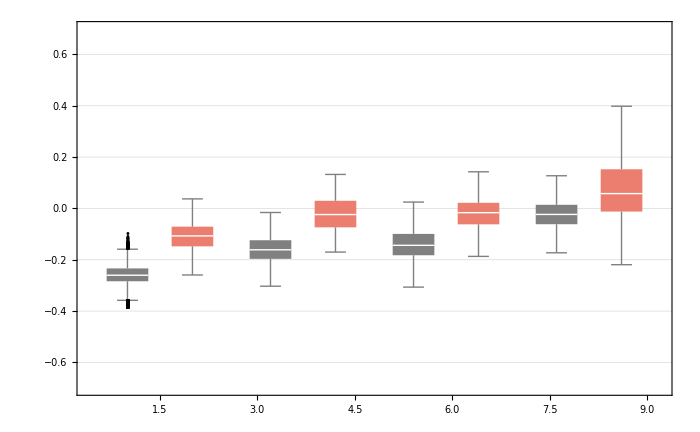

```mathematica
moranIndexSigSelectedEM=BoxWhiskerChart[plotDataAllEM,{"Outliers"},ImageSize->700,PlotRange->{-0.7,0.7},ChartStyle->colourMoran/@Range[2],ChartLabels->{Join[{"Nearest \nneighbour"},ToString/@{0.05,0.15,0.85}],None},FrameLabel-> {None,"Moran index (early and mid stage)"},FrameStyle->Directive[Black,20],GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moranValuesSigSelectedEM.png"}],moranIndexSigSelectedEM]
```

```mathematica
legendMoranSigAll=SwatchLegend[colourMoran/@Range[2],(Style[#,14]&/@{"without cell division","with cell division"})]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","legendMoranSigAll.png"}],legendMoranSigAll]
```